```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Monochromatic

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
σ2=kpeak^2;σ2//N
```

0.154213

### direct sampling

```mathematica
Lpeakdata=Import["data/mono_Lpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
HighLdata=Select[Lpeakdata,#[[4]]>4σ2&];
```

```mathematica
Cpeakdata=Import["data/mono_Cpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
HighCdata=Select[Cpeakdata,#[[5]]>0.45&];
```

```mathematica
pairs=Select[Tuples[{HighLdata,HighCdata}],Max[Abs[#[[1,{1,2,3}]]-#[[2,{2,3,4}]]]]<=1&];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInL=Select[HighLdata,Function[a,!AnyTrue[HighCdata,matchQ[a,#]&]]];
onlyInC=Select[HighCdata,Function[b,!AnyTrue[HighLdata,matchQ[#,b]&]]]
```

{}

```mathematica
DC=HistogramList[Cpeakdata[[All,5]]][[1,2]]-HistogramList[Cpeakdata[[All,5]]][[1,1]];
Cmin=Mean[HistogramList[Cpeakdata[[All,5]]][[1,1;;2]]];
nCLat=Table[{Cmin+DC(i-1),(HistogramList[Cpeakdata[[All,5]]][[2,i]])/(DC NL^3)},{i,Length[HistogramList[Cpeakdata[[All,5]]][[2]]]}];
```

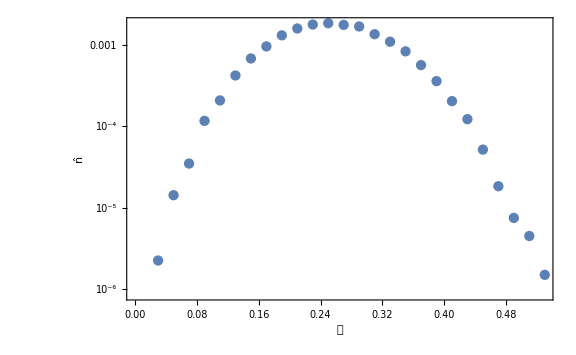

```mathematica
ListLogPlot[nCLat,Joined->False,FrameLabel->{𝒞,OverHat[n]}]
```

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

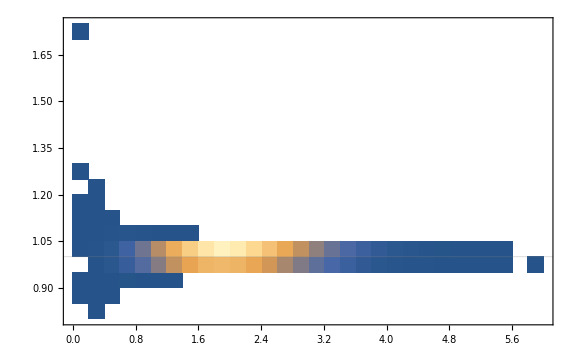

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

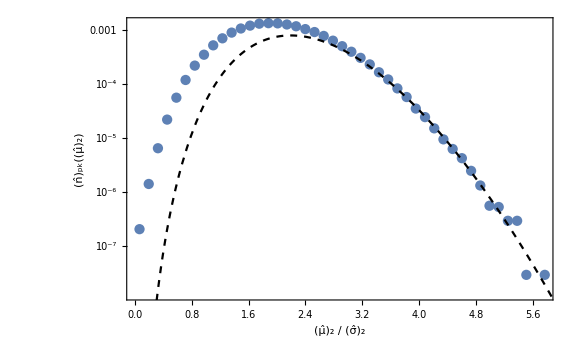

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```